```mathematica
Clear[LEFT,SL,SR,β,T1]
```

```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[22],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,13,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[22],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[22],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[22]-B.ConjugateTranspose[T1].J.T1].B,25000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[22]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[22]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[22]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[22]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

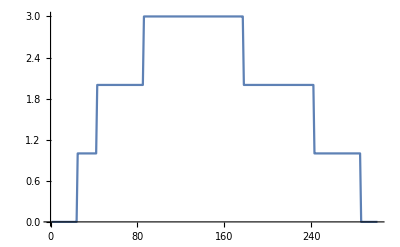

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
ListLinePlot[Table[tr[ω,0.0001,1,0],{ω,0,3,0.01}]]
```

```mathematica
β81[ω_,δ_,t_,ϵ_]:=
ReplacePart[β[ω,δ,t,ϵ],Join[{{7,15},{15,16},{16,17},{17,18},{18,8}},Transpose[{Transpose[{{7,15},{15,16},{16,17},{17,18},{18,8}}][[2]],Transpose[{{7,15},{15,16},{16,17},{17,18},{18,8}}][[1]]}]]->-t]
```

```mathematica
β82[ω_,δ_,t_,ϵ_]:=
ReplacePart[β[ω,δ,t,ϵ],Join[{{14,15},{15,16},{16,17},{17,18},{18,1}},Transpose[{Transpose[{{14,15},{15,16},{16,17},{17,18},{18,1}}][[2]],Transpose[{{14,15},{15,16},{16,17},{17,18},{18,1}}][[1]]}]]->-t]
```

```mathematica
β91[ω_,δ_,t_,ϵ_]:=
ReplacePart[β[ω,δ,t,ϵ],Join[{{7,15},{15,16},{16,17},{17,18},{18,8},{1,22},{22,21},{21,20},{20,19},{19,14}},Transpose[{Transpose[{{7,15},{15,16},{16,17},{17,18},{18,8},{1,22},{22,21},{21,20},{20,19},{19,14}}][[2]],Transpose[{{7,15},{15,16},{16,17},{17,18},{18,8},{1,22},{22,21},{21,20},{20,19},{19,14}}][[1]]}]]->-t]
```

```mathematica
m[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={{imp7,imp4,imp,imp10,imp6,imp3,imp11,imp,imp13,imp,imp14,imp1,imp8,imp6,imp,imp11,imp11,imp3,imp,imp2,imp,imp,imp1,imp8,imp3,imp7,imp6,imp5,imp,imp,imp12,imp11,imp10,imp13,imp,imp,imp10,imp9,imp,imp9,imp,imp4,imp,imp,imp13,imp1,imp,imp,imp,imp,imp,imp,imp,imp5,imp14,imp14,imp2,imp4,imp,imp,imp,imp4,imp,imp12,imp,imp,imp,imp,imp7,imp,imp,imp12,imp10,imp9,imp9,imp13,imp,imp,imp7,imp,imp2,imp5,imp3,imp8,imp2,imp,imp1,imp,imp14,imp6,imp,imp,imp,imp,imp8,imp5,imp,imp,imp,imp12}};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[22]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[22]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[22]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>3,3,tra1]]
```

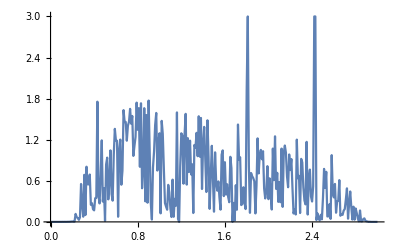

```mathematica
ListLinePlot[Table[{ω,m[ω,0.5]},{ω,Range[0,3,0.01]}]]
```

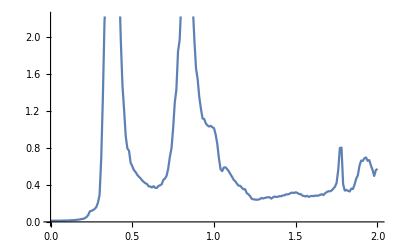

```mathematica
ListPlot[%44,Joined->True]
```

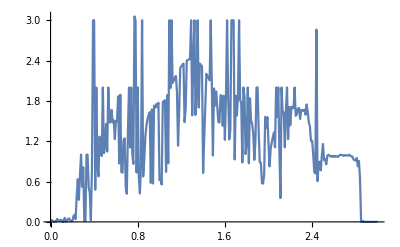

```mathematica
ListLinePlot[Table[{ω,m[ω,0]},{ω,Range[0,3,0.01]}]]
```

```mathematica
RandomSample[Join[Flatten[Table[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},4]],Table[imp,100-(14*4)]]]
```

{imp7,imp4,imp,imp10,imp6,imp3,imp11,imp,imp13,imp,imp14,imp1,imp8,imp6,imp,imp11,imp11,imp3,imp,imp2,imp,imp,imp1,imp8,imp3,imp7,imp6,imp5,imp,imp,imp12,imp11,imp10,imp13,imp,imp,imp10,imp9,imp,imp9,imp,imp4,imp,imp,imp13,imp1,imp,imp,imp,imp,imp,imp,imp,imp5,imp14,imp14,imp2,imp4,imp,imp,imp,imp4,imp,imp12,imp,imp,imp,imp,imp7,imp,imp,imp12,imp10,imp9,imp9,imp13,imp,imp,imp7,imp,imp2,imp5,imp3,imp8,imp2,imp,imp1,imp,imp14,imp6,imp,imp,imp,imp,imp8,imp5,imp,imp,imp,imp12}